# 4 Basic Graph Problems

This notebook describes the 4 basic graph problems: Clique number, Independence number, Graph Coloring, Clique covering Number. TODO: relationships between all 4.

## Clique Number

A clique is a collection of vertices such that each pair of vertices is adjacent. The clique number is the size of the largest clique.

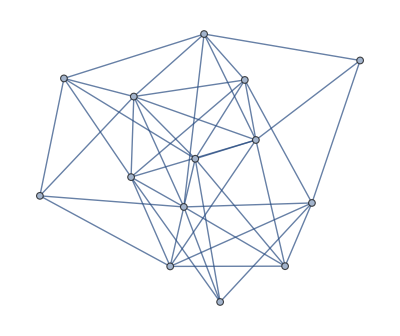

```mathematica
G=RandomGraph[{14,Floor[Binomial[15,2]/2]-10}]
```

```mathematica
FindClique[G] (*Returns a maximum clique in the graph.*)
```

{{1,2,11,12}}

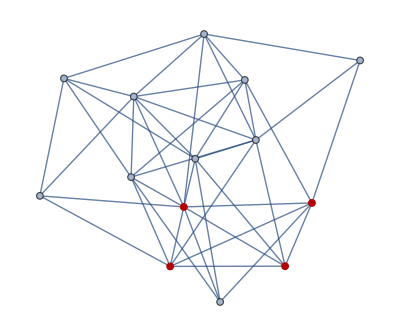

```mathematica
HighlightGraph[G,FindClique[G]]
```

## Independence Number

An independent set is a set of vertices such that no pair is adjacent. The independence number is the size of the largest independent set.

```mathematica
FindIndependentVertexSet[G]
```

{{6,8,9,10,11}}

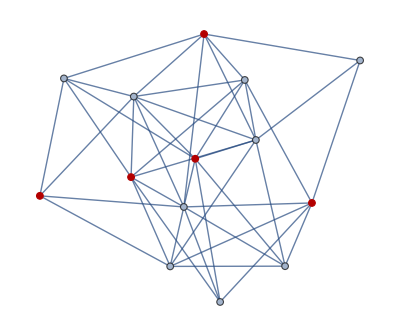

```mathematica
HighlightGraph[G,FindIndependentVertexSet[G]]
```

Basic fact: The independence number is the clique number of the complement of the graph:

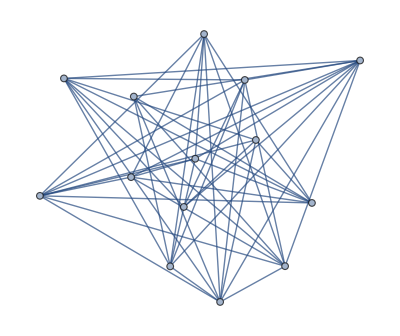

```mathematica
GComplement=GraphComplement[G]
```

```mathematica
HighlightGraph[G,FindClique[GComplement]]
```

-Graphics-

## Coloring Number

The coloring number of a graph is the smallest number of colors needed to  color the vertices of the graph so that no two adjacent vertices have the same color.

```mathematica
FindVertexColoring[G] (*Colors G*)
```

{2,4,1,2,2,3,1,3,3,3,3,1,4,2}

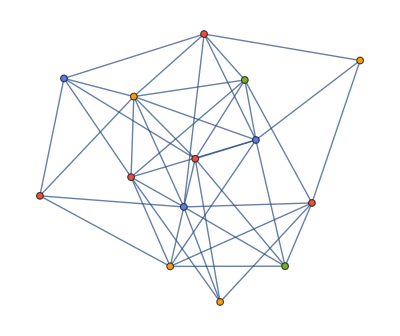

```mathematica
Annotate[G,{VertexStyle->Thread[VertexList[G]->(FindVertexColoring[G,ColorData[106,"ColorList"]])]}] (*Draws G with the coloring*)
```

Notice that every color is an independent set, and each vertex is assigned a color. This shows that the product of the independence number and coloring number is at least as large as the number of vertices.

## Clique Covering Number

The clique covering number is the smallest number of disjoint cliques that contain each vertex. It is the coloring number of the complement graph. Mathematica does not have a builtin function for it.

```mathematica
FindVertexColoring[GComplement]
```

{4,4,1,3,1,3,3,1,2,5,4,2,5,2}

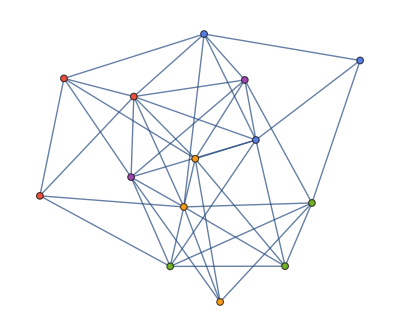

```mathematica
Annotate[G,{VertexStyle->Thread[VertexList[G]->(FindVertexColoring[GComplement,ColorData[106,"ColorList"]])]}]
```

## Lack of relationship between clique number and chromatic number

See https : // mathworld.wolfram.com/MycielskiGraph.html

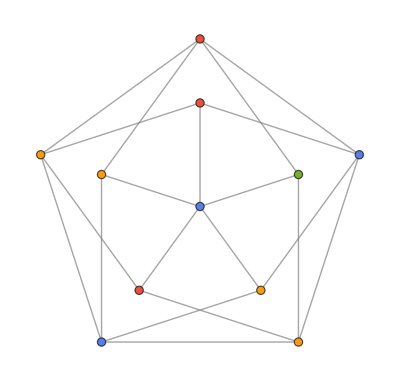

```mathematica
A=FromEntity[Entity["Graph",{"Mycielski",4}]];
Annotate[A,{VertexStyle->Thread[VertexList[A]->(FindVertexColoring[A,ColorData[106,"ColorList"]])]}]
```